```mathematica
Needs["utilities`"]
Get[FileNameJoin@{NotebookDirectory[],"generalizedKlyshkoCriteria.m"}]

ClearAll[displacedFockProbs,addNoiseToProb];
displacedFockProbs[k_List,μ_,l_]:=displacedFockProbs[#,μ,l]&/@k;
displacedFockProbs[k_,μ_,l_]:=ⅇ^-μ μ^(k-l) (k!)/(l!)Sum[Binomial[l,j](-μ)^j/((k-l+j)!),{j,Max[l-k,0],l}]^2;

addNoiseToProb[k_List,μ_,probVec_List]:=addNoiseToProb[#,μ,probVec]&/@k;
addNoiseToProb[k_,μ_,probVec_List]:=Sum[probVec⟦idx⟧displacedFockProbs[k,μ,idx-1],{idx,Range@Length@probVec}];
```

```mathematica
displacedFockProbs[k,μ,1]//FullSimplify[#,{k,n}∈Integers&&k>0&&n≥0]&
```

(ⅇ^-μ (k-μ)^2 μ^(-1+k))/(k!)

```mathematica
displacedFockProbs[{0,1,2},μ,1]
```

{ⅇ^-μ μ,ⅇ^-μ (1-μ)^2,2 ⅇ^-μ (1-μ/2)^2 μ}

```mathematica
displacedFockProbs[0,μ,2]
Sum[
Simplify[displacedFockProbs[k,μ,2],k∈Integers&&k>0],
{k,1,Infinity}
]//Simplify
```

1/2 ⅇ^-μ μ^2

1-1/2 ⅇ^-μ μ^2

```mathematica
addNoiseToProb[2,μ,{0,1,0}]
```

2 ⅇ^-μ (1-μ/2)^2 μ

```mathematica
addNoiseToProb
```

```mathematica
displacedFockProbs[0,μ,1]
displacedFockProbs[1,μ,1]
displacedFockProbs[2,μ,1]
```

ⅇ^-μ μ

ⅇ^-μ (1-μ)^2

2 ⅇ^-μ (1-μ/2)^2 μ

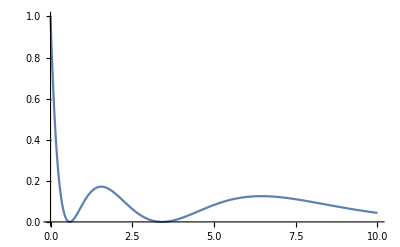

```mathematica
Plot[displacedFockProbs[2,μ,2],{μ,0,10},PlotRange->All]
```

### Visualise the Fock distribution of displaced Fock states

```mathematica
Manipulate[
DiscretePlot[displacedFockProbs[k,μ,1],{k,0,20},PlotRange->All,Joined->True,PlotMarkers->Automatic,PerformanceGoal->"Quality"],
{{μ,1},0.01,20,0.01,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
DiscretePlot[displacedFockProbs[k,μ,2],{k,0,20},PlotRange->All,Joined->True,PlotMarkers->Automatic,PerformanceGoal->"Quality"],
{{μ,0.01},0.01,20,0.01,Appearance->"Labeled"}]
```

Klyshko says that for μ=1 the displaced Fock |1⟩ is classical:

```mathematica
N@klyshkoBasicCriteria[1,displacedFockProbs[{0,1,2},1,1]]
```

-0.135335

### Adding noise to displaced (noisy) Fock states

```mathematica
With[{μ=1},With[
{probDistro=Table[N@displacedFockProbs[k,μ,1],{k,0,10}]},
noisyDisplacedFock1=Table[
addNoiseToProb[k,μ,probDistro],
{k,0,20}
]
]];
```

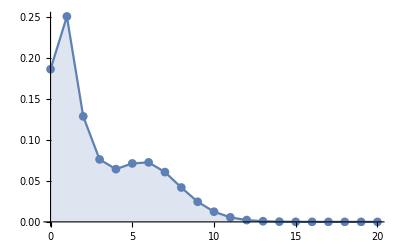

```mathematica
With[{μ=1},With[
{probDistro=Table[N@displacedFockProbs[k,μ,1],{k,0,10}]},
DiscretePlot[
addNoiseToProb[k,μ,probDistro],
{k,0,20},PlotRange->All,Joined->True,PlotMarkers->Automatic
]
]]
```

## Klyshko nonclassicality of “doubly displaced” states

```mathematica
ClearAll@doubleDisplacedFock1;
doubleDisplacedFock1[n_Integer,firstμ_,secondμ_,truncation_:30]:=addNoiseToProb[n,secondμ,
Table[N@displacedFockProbs[k,firstμ,1],{k,0,truncation}]
];
doubleDisplacedFock1[ns_List,firstμ_,secondμ_,truncation_:30]:=doubleDisplacedFock1[#,firstμ,secondμ,truncation]&/@ns;
```

Klyshko says that for μ=1 the displaced Fock |1⟩ is classical:

```mathematica
doubleDisplacedFock1[{0,1,2},1,1]//klyshkoBasicCriteria[1,#]&
```

0.0148914

```mathematica
N@klyshkoBasicCriteria[1,noisyDisplacedFock1]
```

0.0148914

```mathematica
klyshkoNonclassicalities=Table[
{firstN,secondN,klyshkoBasicCriteria[1,#]&@doubleDisplacedFock1[{0,1,2},firstN,secondN]},{secondN,0.001,2,0.01},{firstN,0.001,2,0.01}
];
```

```mathematica
klyshkoNonclassicalitiesDetailed=Table[
{firstN,secondN,klyshkoBasicCriteria[1,#]&@doubleDisplacedFock1[{0,1,2},firstN,secondN,40]},{secondN,0.001,3,0.01},{firstN,0.001,2,0.01}
];
```

```mathematica
With[{data={#⟦1⟧,#⟦2⟧,Sign@#⟦3⟧}&/@Flatten[klyshkoNonclassicalities,1]},
ListDensityPlot[data,InterpolationOrder->0,FrameLabel->{"firstN","secondN"},ColorFunction->"TemperatureMap"]
]
```

-Graphics-

```mathematica
With[{data=Flatten[klyshkoNonclassicalities,1]},
ListContourPlot[data,FrameLabel->{"firstN","secondN"},ColorFunction->"TemperatureMap",PlotLegends->Automatic]
]
```

-Graphics-

```mathematica
With[{data=Flatten[klyshkoNonclassicalities,1]},
ListPlot3D[data,AxesLabel->{"firstN","secondN","K"},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->{All,0.3}
]~Show~Graphics3D[{Opacity@0.4,Red,InfinitePlane@{{0,0,0},{0,1,0},{1,0,0}}}]
]
```

-Graphics3D-

```mathematica
Graphics3
```